```mathematica
FactInteger[n_]:=If[n==1,{},FactorInteger[n]]
d[n_,z_]:=Product[1/(j[[2]]!) Pochhammer[z,j[[2]]],{j,FactInteger[n]}]
```

```mathematica
d[100,3]
```

36

```mathematica
dl[n_,z_]:=Sum[Log[1/(j[[2]]!) Pochhammer[z,j[[2]]]],{j,FactInteger[n]}]
```

```mathematica
dl[30,3]
```

3 Log[3]

```mathematica
N[Log[d[100,3]]]
```

3.58352

```mathematica
FullSimplify[Log[1/(a!) Pochhammer[z,a]]]
```

Log[Pochhammer[z,a]/(a!)]

```mathematica
FullSimplify[Log[Binomial[a,b]]]
```

Log[Binomial[a,b]]

```mathematica
DD[n_, z_ ]:=Sum[d[j,z],{j,1,n}]
```

```mathematica
DD[100,2]
```

482

```mathematica
DM[n_, z_] := Sum[ d[j,-1]DD[Floor[n/j],z+1],{j,1,n}]
```

```mathematica
DD[100,I]
```

-2881/72+(65 ⅈ)/8

```mathematica
DM[100,I]
```

-2881/72+(65 ⅈ)/8

```mathematica
Table[{n,MoebiusMu[n],d[n,-1]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | -1 | -1
3 | -1 | -1
4 | 0 | 0
5 | -1 | -1
6 | 1 | 1
7 | -1 | -1
8 | 0 | 0
9 | 0 | 0
10 | 1 | 1
11 | -1 | -1
12 | 0 | 0
13 | -1 | -1
14 | 1 | 1
15 | 1 | 1
16 | 0 | 0
17 | -1 | -1
18 | 0 | 0
19 | -1 | -1
20 | 0 | 0
21 | 1 | 1
22 | 1 | 1
23 | -1 | -1
24 | 0 | 0
25 | 0 | 0
26 | 1 | 1
27 | 0 | 0
28 | 0 | 0
29 | -1 | -1
30 | -1 | -1
31 | -1 | -1
32 | 0 | 0
33 | 1 | 1
34 | 1 | 1
35 | 1 | 1
36 | 0 | 0
37 | -1 | -1
38 | 1 | 1
39 | 1 | 1
40 | 0 | 0
41 | -1 | -1
42 | -1 | -1
43 | -1 | -1
44 | 0 | 0
45 | 0 | 0
46 | 1 | 1
47 | -1 | -1
48 | 0 | 0
49 | 0 | 0
50 | 0 | 0
51 | 1 | 1
52 | 0 | 0
53 | -1 | -1
54 | 0 | 0
55 | 1 | 1
56 | 0 | 0
57 | 1 | 1
58 | 1 | 1
59 | -1 | -1
60 | 0 | 0
61 | -1 | -1
62 | 1 | 1
63 | 0 | 0
64 | 0 | 0
65 | 1 | 1
66 | -1 | -1
67 | -1 | -1
68 | 0 | 0
69 | 1 | 1
70 | -1 | -1
71 | -1 | -1
72 | 0 | 0
73 | -1 | -1
74 | 1 | 1
75 | 0 | 0
76 | 0 | 0
77 | 1 | 1
78 | -1 | -1
79 | -1 | -1
80 | 0 | 0
81 | 0 | 0
82 | 1 | 1
83 | -1 | -1
84 | 0 | 0
85 | 1 | 1
86 | 1 | 1
87 | 1 | 1
88 | 0 | 0
89 | -1 | -1
90 | 0 | 0
91 | 1 | 1
92 | 0 | 0
93 | 1 | 1
94 | 1 | 1
95 | 1 | 1
96 | 0 | 0
97 | -1 | -1
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0

```mathematica
DM2[n_, z_, k_] := Sum[ d[j,k]DD[Floor[n/j],z-k],{j,1,n}]
```

```mathematica
DD[334,2.4I]
```

45.3394-765.029 ⅈ

```mathematica
DM2[334,2.4I,7.2+3.2I]
```

45.3394-765.029 ⅈ

```mathematica
DH[n_,k_,s_]:=Sum[Binomial[k,k-j] DH[n/m^j,k-j,m+1],{m,s,n^(1/k)},{j,1,k}]
DH[n_,0,s_]:=1
```

```mathematica
DH[100,2,1]
```

482

```mathematica
DDH[x_] := 2 Sum[Floor[x/k],{k,1,Floor[x^(1/2)]}]-Floor[x^(1/2)]^2

DH[n,1,1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

```mathematica
DDH[100]
```

482

```mathematica
DH[120,1,1]
```

120

```mathematica
DD[100,4]
```

3575

```mathematica
DF[k_,n_,s_]:=If[ s > n^(1/k),0,Sum[Binomial[k,j] DF[k-j,Floor[n/s^j],s+1],{j,0,k}]]
DF[0,n_,s_]:=1
```

```mathematica
DF[3,100,1]
```

1471

```mathematica
DR[k_,n_,s_]:=If[ s > n^(1/k),0,Sum[ If[ N[Binomial[k,k-j]]<.1,0,Binomial[k,k-j] DR[k-j,Floor[n/s^j],s+1]],{j,0,k}]]
DR[0,n_,s_]:=1
```

```mathematica
DR[3.5,100,1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

1. (0.+2.1875 Binomial[0.5,0.5] If[Hold[128>12^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[12/128^j],128+1]]])+3.5 (0.+2.5 (1. (0.+1.5 Binomial[0.5,0.5] If[Hold[128>12^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[12/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>16^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[16/128^j],128+1]]])+1.875 Binomial[0.5,0.5] If[Hold[128>25^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[25/128^j],128+1]]])+4.375 (1. (1. (1. (1. (1. (1. (0.+1.5 Binomial[0.5,0.5] If[Hold[128>12^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[12/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>14^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[14/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>16^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[16/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>20^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[20/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>25^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[25/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>33^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[33/128^j],128+1]]])+1.5 Binomial[0.5,0.5] If[Hold[128>50^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[50/128^j],128+1]]])+2.1875 Binomial[0.5,0.5] If[Hold[128>100^(1/0.5)],0,∑_(j=0)^0.5 If[N[Binomial[0.5,0.5-j]]<0.1,0,Binomial[0.5,0.5-j] DR[0.5-j,Floor[100/128^j],128+1]]]

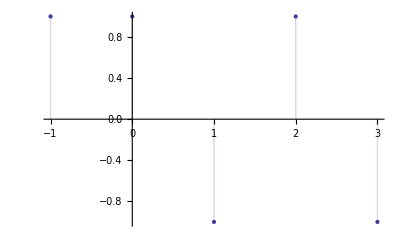

```mathematica
DiscretePlot[Binomial[-1,n],{n,-1, 3}]
```

```mathematica
Binomial[-1,-2]
```

-1

```mathematica
Expand[(x+1)^6]
```

1+6 x+15 x^2+20 x^3+15 x^4+6 x^5+x^6

```mathematica
Table[ Binomial[ 6,j],{j,0,6}]
```

```mathematica
{1,6,15,20,15,6,1}
```

```mathematica
Expand[(x+1)^(11/3)]
```

(1+x)^(2/3)+3 x (1+x)^(2/3)+3 x^2 (1+x)^(2/3)+x^3 (1+x)^(2/3)

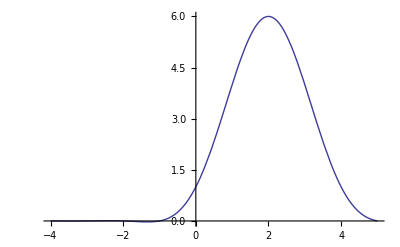

```mathematica
Plot[Binomial[4,n],{n,-4,5}]
```

```mathematica
Bin[x_, y_ ] := Gamma[ x+1]/( Gamma[y+1] Gamma[ x-y+1] )
```

```mathematica
N[Bin[2.5, 2 I]]
```

-7.1986+9.77265 ⅈ

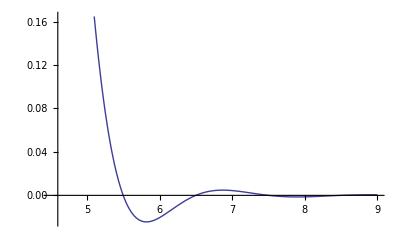

```mathematica
Plot[Binomial[4.5,n],{n,4.5,9}]
```

```mathematica
Binomial[4.5,0]
```

1.

```mathematica
d[100,-15.5]
```

12628.1

```mathematica
Binomial[5.5,15.5]
```

0.

```mathematica
Sum[ d[10,2.25-k] Binomial[2.25,k] (-1)^(k-1),{k,0,11128}]
```

-0.223456